Weather simulation using a Markov State model. Given a state transition matrix , the probability on day  is given by .
Based on Steve Brunton’s excellent “Gentle introduction to Modeling with Matrices and Vectors: A probabilistic weather model” at https://www.youtube.com/watch?v=K-8F_zDMDUI

```mathematica
A=({{0.5, 0.5, 0.25}, {0.25, 0, 0.25}, {0.25, 0.5, 0.5}});
x[0]=({{1}, {0}, {0}});
x[t_]:=A . x[t-1];
n=25;
x[n] // TraditionalForm
```

(0.4
0.2
0.4)

The final prediction is .Check the quality of convergence by the difference between the last two steps (smaller is better).

```mathematica
convergence=Max[Abs[x[n]-x[n-1]]]
```

1.77636×10^-15

...ok that’s pretty dang small. From what we know about MSMs, they should converge such that the steady state probability lies on the eigenvector corresponding to the eigenvalue 1. It’s easiest to show this if it is normalised such that its components add up to 1.

```mathematica
{eivals,eivects}=Eigensystem[A];
eivals[[1]]
eivects[[1]]
```

1.

{-0.666667,-0.333333,-0.666667}

```mathematica
eivects[[1]]/Total[eivects[[1]]]
```

{0.4,0.2,0.4}

OK cool.  Now we plot it something like this

```mathematica
rainy=Flatten[(x[#][[1]])& /@ Range[n]];
nice=Flatten[(x[#][[2]])& /@ Range[n]];
cloudy=Flatten[(x[#][[3]])& /@ Range[n]];
```

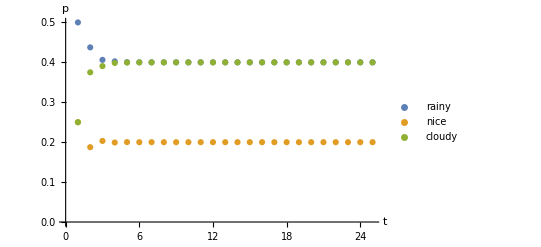
-Graphics-Weather probability in Seattle vs time

```mathematica
Labeled[
ListPlot[{rainy,nice,cloudy},
AxesLabel->{"t","p"},
PlotLegends->{"rainy","nice","cloudy"}
],
"Weather probability in Seattle vs time"
]
```